```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
customGamma[a_,b_]:= GammaDistribution[a,1/b]
```

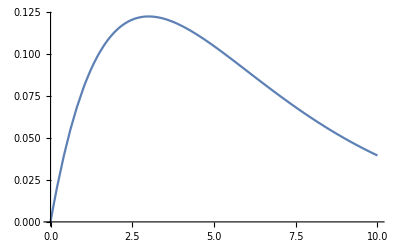

```mathematica
Plot[PDF[customGamma[2,1/3],x],{x,0,10}]
```

```mathematica
data=RandomVariate[customGamma[2,1/3],{10}];
```

```mathematica
data={5.0532552676071845,7.8351912827194905,3.4444796234812127,3.1790918878506687,4.338775692646351,5.1879847309262335,8.066098907681695,3.674751168626843,2.3308744166104014,6.3004204747870105};
```

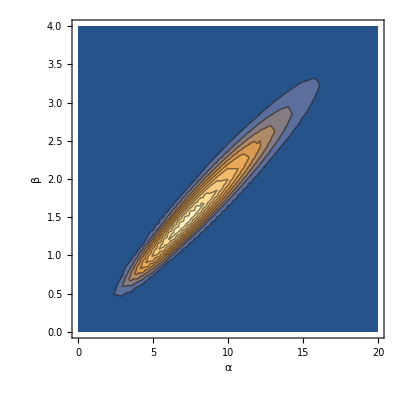

```mathematica
g1=ContourPlot[Likelihood[customGamma[α,β],data],{α,0,20},{β,0,4},PlotRange->Full,Frame->{True,True,False,False},FrameLabel->{"α","β"},BaseStyle->Medium]
```

```mathematica
Clear[μ,σ]
```

```mathematica
Solve[{μ == Mean@customGamma[a,b], σ ^2 == Variance@customGamma[a,b]},{a,b}]
```

{{a→μ^2/σ^2,b→μ/σ^2}}

```mathematica
customGamma1[μ_,σ_]:= Module[{a=μ^2/σ^2,b=μ/σ^2},customGamma[a,b]]
```

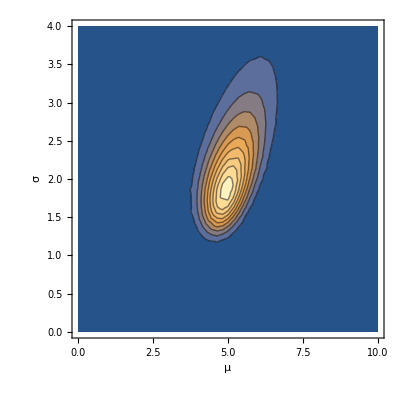

```mathematica
g2=ContourPlot[Likelihood[customGamma1[μ,σ],data],{μ,0,10},{σ,0,4},PlotRange->Full,Frame->{True,True,False,False},FrameLabel->{"μ","σ"},BaseStyle->Medium]
```

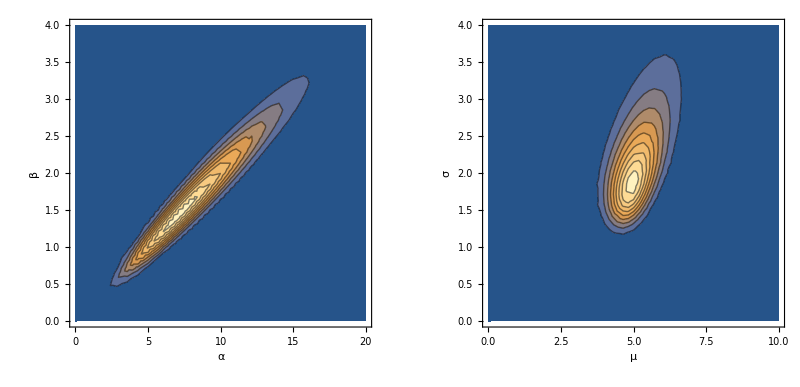

```mathematica
gFinal=Show[GraphicsRow[{g1,g2}],ImageSize->800]
```

```mathematica
Export["Distributions_gammaLotteryLikelihood.pdf",gFinal]
```

Distributions_gammaLotteryLikelihood.pdf

```mathematica
PDF[customGamma1[μ,σ],x]
```

Piecewise[{{(ⅇ^(-(x μ)/σ^2) x^(-1+μ^2/σ^2) (σ^2/μ)^(-μ^2/σ^2))/Gamma[μ^2/σ^2], x>0}, {0, True}}]

```mathematica
(ⅇ^(-(x μ)/σ^2) x^(-1+μ^2/σ^2) (σ^2/μ)^(-μ^2/σ^2))/Gamma[μ^2/σ^2]//TeXForm
```

\frac{\left(\frac{\sigma ^2}{\mu }\right)^{-\frac{\mu ^2}{\sigma ^2}} e^{-\frac{\mu  x}{\sigma ^2}} x^{\frac{\mu ^2}{\sigma ^2}-1}}{\Gamma \left(\frac{\mu
   ^2}{\sigma ^2}\right)}